# Wavelets for Quantum Field Theory

## Convenience Functions

```mathematica
sparseIdentityMtx[size_Integer]:=SparseArray[Band[{1,1}]->1,{size,size}];

zeroMtx[size_Integer]:=SparseArray[{},{size,size}];

symplecticMtx[size_?EvenQ]:=ArrayFlatten[{{zeroMtx[size/2],sparseIdentityMtx[size/2]},{-sparseIdentityMtx[size/2],zeroMtx[size/2]}}];

blockDiagMtx[mtx_List]/;And@@MatrixQ/@mtx:=
Module[{out=zeroMtx[Length[mtx]]},
Do[out[[k,k]]=mtx[[k]],{k,Length[mtx]}];
ArrayFlatten[out]];

blockAntiDiagMtx[mtx_List]/;And@@MatrixQ/@mtx:=
Module[{out=zeroMtx[Length[mtx]]},
Do[out[[k,Length[mtx]+1-k]]=mtx[[k]],{k,Length[mtx]}];
ArrayFlatten[out]];

symplecticDiagonalization[mtx_?AntisymmetricMatrixQ]:=
Module[{vals,vecs,locations,out},
{vals,vecs}=Eigensystem[mtx];
vals=Chop[Im[vals]];
With[
{positiveLocations=Flatten[Position[vals,_?Positive]],
zeroLocations=Flatten[Position[vals,0]][[;;;;2]]},
locations=Join[positiveLocations,zeroLocations];
];
With[
{B=Orthogonalize[vecs[[locations]]]},
out=Orthogonalize[Join[Re[B],Im[B]]];
];
out];
```

## Derivative Overlap Coefficients

```mathematica
derivativeOverlaps[M_Integer/;M≥2, n_Integer/;n>0]/;M≥(n+1)/2:=
Module[{a,x,eqns,vars,soln},

(* autocorrelation coefficients *)
c=((2*M-1)!/((M-1)!*4^(M-1)))^2;

a[k_Integer/;k>0]:=If[OddQ[k]&&k≤2M-1,
With[{m=(k+1)/2},((-1)^(m-1)*c)/((2 m-1)(M-m)! (M+m-1)!)],0];

(* set of equations in *)
eqns=Table[x[l]==2^n(x[2l]+1/2 Sum[a[2k-1] (x[2l-2k+1]+x[2l+2k-1]),{k,M}]),
{l,2-2M,2M-2}]/.{x[l_/;Abs[l]>2 M-2]:>0};

AppendTo[eqns,Sum[l^n x[l],{l,-2 M+2,2 M-2}]==(-1)^n n!];

vars=x/@Range[-2 M+2,2 M-2];
soln=Solve[eqns,vars][[1]];
Lookup[soln,x[#],0]&];
```

## Derivative Matrix in Fixed-Scale Wavelet Basis

```mathematica
derivativeMtx[M_Integer/;M≥2,n_Integer/;n>0,
boundary_String/;StringMatchQ[boundary,{"open","periodic"}],
prec_:MachinePrecision][size_Integer]:=
With[{dVec = derivativeOverlaps[M, n]},
If[boundary=="open",
SparseArray[Join[
{Band[{1,1}]->dVec[0]},
Table[Band[{1, k+1}]->dVec[k],{k,1,2 M-2}],
Table[Band[{k+1,1}]->dVec[-k],{k,1,2M-2}]],{size,size}],
If[boundary=="periodic",
 SparseArray[Join[
{Band[{1,1}]->dVec[0]},
Table[Band[{1, k+1}]->dVec[k],{k,1,2 M-2}],
Table[Band[{1,size+1-k}]->dVec[-k],{k,1,2 M-2}],
Table[Band[{k+1,1}]->dVec[-k],{k,1,2M-2}],
Table[Band[{size+1-k,1}]->dVec[k],{k,1,2M-2}]],{size,size}],
If[boundary=="antiperiodic",
 SparseArray[
Join[
{Band[{1,1}]->dVec[0]},
Table[Band[{1, k+1}]->dVec[k],{k,1,2 M-2}],
Table[Band[{1, size+1-k}]->-dVec[-k],{k,1,2 M-2}],
Table[Band[{k+1,1}]->dVec[-k],{k,1,2M-2}],
Table[Band[{size+1-k,1}]->-dVec[k],{k,1,2M-2}]
],
{size,size}]
]
]]];
```

## Wavelet Decomposition Matrix

```mathematica
vecToRules[vec_,size_]:=
Flatten@Table[
Table[
Rule[{k+1,2k+l},vec[[l]]],
{l,Length[vec]}],
{k,0,size/2-1}]

partitionRules[rules_,threshold_]:=
{Select[rules,#[[1,2]]≤threshold&],
Select[rules,#[[1,2]]>threshold&]};

periodizeRules[rules_,threshold_]:=
(Rule[#1-{0,threshold},#2]&)@@@rules;

filterMatrixRules[size_,vec_]:=
Module[{rules,mainRules,edgeRules},
rules=vecToRules[vec,size];
{mainRules,edgeRules}=partitionRules[rules,size];
edgeRules=periodizeRules[edgeRules,size];
{mainRules,edgeRules}];

filterMatrixRules[size_,vec_,"open"]:=
filterMatrixRules[size,vec][[1]];

filterMatrixRules[size_,vec_,"periodic"]:=
Join@@filterMatrixRules[size,vec];

filterMatrixRules[size_,vec_,"antiperiodic"]:=
Module[{mainRules,edgeRules},
{mainRules,edgeRules}=filterMatrixRules[size,vec];
Join[mainRules,(Rule[#1,-#2]&)@@@edgeRules]];

filterMatrix[size_Integer,vec_?VectorQ,boundary_?StringQ]:=
SparseArray[filterMatrixRules[size,vec,boundary]];

lowpassMtx[wave_,boundary_?StringQ][size_]:=
With[{vec=Sqrt[2]*WaveletFilterCoefficients[wave,"PrimalLowpass"][[;;,2]]},
filterMatrix[size,vec,boundary]];

hipassMtx[wave_,boundary_?StringQ][size_]:=
With[{vec=Sqrt[2]*WaveletFilterCoefficients[wave,"PrimalHighpass"][[;;,2]]},
filterMatrix[size,vec,boundary]];

WTM[wave_,boundary_?StringQ][size_?EvenQ]:=
ArrayFlatten[
{{lowpassMtx[wave,boundary][size]},
{hipassMtx[wave,boundary][size]}}];

WTM[wave_,boundary_?StringQ][size_Integer,0]:=
sparseIdentityMtx[size];

WTM[wave_,boundary_?StringQ][size_Integer,1]:=
WTM[wave,boundary][size];

WTM[wave_,boundary_?StringQ][size_Integer,level_Integer]:=
With[{W=WTM[wave,boundary],sI=sparseIdentityMtx},
Fold[#2.#1&,W[size],
Table[blockDiagMtx[{W[size/2^k],sI[size-size/2^k]}],
{k,level-1}]]];
```

# Bosonic Theory

## Bosonic Coupling Matrix in Fixed-Scale Wavelet Basis

```mathematica
coupMtxBosonic[waveletIndex_Integer/;waveletIndex≥3,mass_?NumericQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],prec_:MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer]:=
With[{size=baseScaleModes*2^scaleIndex},
mass^2*sparseIdentityMtx[size]-(4^scaleIndex)*derivativeMtx[waveletIndex,2,boundary][size]];
```

## Bosonic Coupling Matrix in Multi-Scale Wavelet Basis

```mathematica
With[{dbIndex=3,boundary="periodic",baseScaleModes=20,scaleIndex=5,mass=1},
Kss=coupMtxBosonic[dbIndex,mass,boundary][baseScaleModes,scaleIndex];
wMtx=WTM[DaubechiesWavelet[dbIndex],"periodic"];
W=wMtx[baseScaleModes*2^scaleIndex,scaleIndex];
Kww=W.Kss.Transpose[W];(* computes multi-scale coupling matrix *)
ICM=MatrixFunction[Sqrt,Kww];(* computes the inverse-covarance matrix(ICM) *)
appICM=Chop[(ICM+Transpose[ICM])/2,10^-5](* computes an approximate ICM *); 
]
```

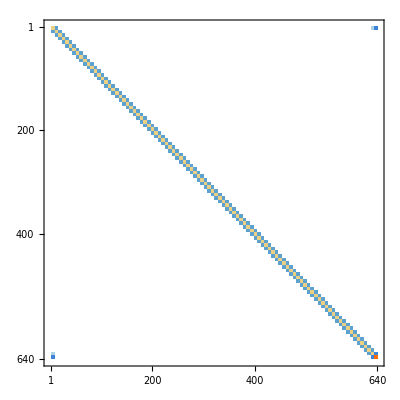

-Graphics-

-Graphics-

-Graphics-

```mathematica
Kss//MatrixPlot
Kww//MatrixPlot
ICM//MatrixPlot
appICM//MatrixPlot
```

## Bosonic Subsystem Covariance Matrix

```mathematica
covMtxBosonic[waveletIndex_Integer/;waveletIndex≥3,mass_?NumericQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],prec_: MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer]:=
Module[{rootK,invrootK,kMtx=N[coupMtxBosonic[waveletIndex,mass,boundary][baseScaleModes*2^scaleIndex],prec]},
rootK=MatrixFunction[Sqrt,kMtx];
invrootK=Inverse[rootK];
blockDiagMtx[{invrootK,rootK}/2]];


diagBlockRowsCovMtxBosonic[waveletIndex_Integer/;waveletIndex≥3,mass_?NumericQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],prec_: MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer]:=
Module[
{rootK,invrootK,kMtx=N[coupMtxBosonic[waveletIndex,mass,boundary][baseScaleModes,scaleIndex],prec]},
rootK=MatrixFunction[Sqrt,kMtx];
invrootK=Inverse[rootK];
{invrootK,rootK}/2];


sysCovMtxBosonic[covMtxDiagBlockRows_]:=blockDiagMtx[covMtxDiagBlockRows];
subsysCovMtxBosonic[covMtxDiagBlockRows_][modeList_]:=blockDiagMtx[#[[modeList,modeList]]&/@covMtxDiagBlockRows]
```

## Bosonic Subsystem Entanglement Entropy

```mathematica
symplecticEigenvalues[covMtx_?MatrixQ/;Equal@@Dimensions[covMtx]] :=
With[{sympMtx=symplecticMtx[Length[covMtx]]},Im[Eigenvalues[sympMtx.covMtx]]];

subsysEntropyBosonic[subsysCovMtx_?MatrixQ /; Equal@@Dimensions[subsysCovMtx]] :=
With[{entropyFunc=If[N[#]>1/2,(#+1/2)Log2[#+1/2]-(#-1/2)Log2[#-1/2],0] &},
Total[entropyFunc/@symplecticEigenvalues[subsysCovMtx]]];
```

```mathematica
With[{dbIndex=3,boundary="open",baseScaleModes=5,scaleIndex=0,mass=1},
diagBlockRowsCovMtxBosonic[dbIndex,mass,boundary][baseScaleModes,scaleIndex]//MatrixForm
]
```

((0.230637
0.0768786
0.0171049
0.00297027
0.00060384) | (0.0768786
0.268955
0.0874789
0.019035
0.00297027) | (0.0171049
0.0874789
0.27228
0.0874789
0.0171049) | (0.00297027
0.019035
0.0874789
0.268955
0.0768786) | (0.00060384
0.00297027
0.0171049
0.0768786
0.230637)
(1.19959
-0.355564
0.039096
-0.000421952
-0.00132039) | (-0.355564
1.14486
-0.358155
0.0395126
-0.000421952) | (0.039096
-0.358155
1.1434
-0.358155
0.039096) | (-0.000421952
0.0395126
-0.358155
1.14486
-0.355564) | (-0.00132039
-0.000421952
0.039096
-0.355564
1.19959))

```mathematica
With[{dbIndex=3, mass=1,baseScaleModes=50,scaleIndex=2, boundary ="open"},
With[{
covMtx=subsysCovMtxBosonic[diagBlockRowsCovMtxBosonic[dbIndex,mass,boundary][baseScaleModes,scaleIndex]],
systemModes=All,
subsystemModes=Range[30]
},
Print["Entropy of whole system: ",subsysEntropyBosonic[covMtx[systemModes]]];
Print["Entropy of subsystem: ",subsysEntropyBosonic[covMtx[subsystemModes]]]
]
]
```

Entropy of whole system: 0

Entropy of subsystem: 0.501503

## Generating Data for Bosonic Entanglement Entropy

```mathematica
genEntropyTableBosonic[waveletIndex_Integer/;waveletIndex≥3,mass_?NumberQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],
prec_:MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer,stepModes_Integer]:=
With[
{covDiags=diagBlockRowsCovMtxBosonic[waveletIndex,mass,boundary,prec][baseScaleModes,scaleIndex],systemModes=baseScaleModes*2^scaleIndex},
Block[{subsystemModes},
Monitor[
Table[{subsystemModes/systemModes,subsysEntropyBosonic[subsysCovMtxBosonic[covDiags][Range[subsystemModes]]]},
{subsystemModes,stepModes,systemModes/2 -stepModes,stepModes}],
ProgressIndicator[subsystemModes/systemModes]]
]];
```

## Bosonic Entanglement Entropy Plots (Periodic Boundary)

Computation of entropies at scale 0 finished in 0 seconds.

Computation of entropies at scale 1 finished in 0 seconds.

Computation of entropies at scale 2 finished in 1 seconds.

Computation of entropies at scale 3 finished in 3 seconds.

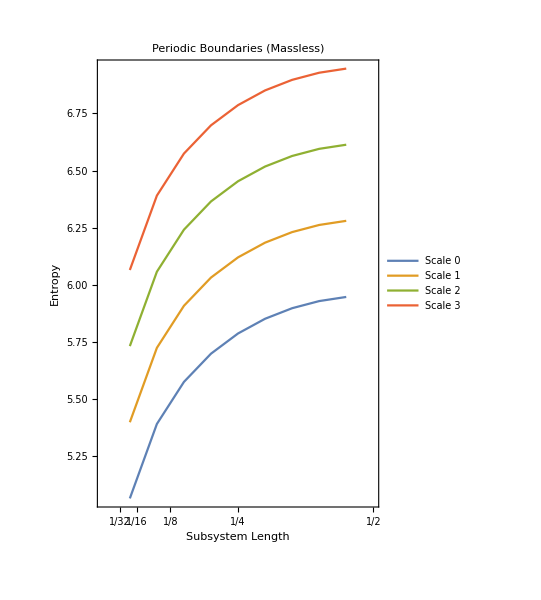

```mathematica
With[{dbIndex=3,boundary="periodic",mass=10^-4,baseScaleModes=100,stepModes=5,numOfScales=4},
data=Table[0,{numOfScales}];
genData=genEntropyTableBosonic[dbIndex,mass,boundary];

Do[
tic=AbsoluteTime[];
With[{maxScale=scaleIndex-1},
data[[scaleIndex]]=genData[baseScaleModes,maxScale,stepModes*2^maxScale]];
toc=AbsoluteTime[];
Print["Computation of entropies at scale ",scaleIndex-1," finished in ",Round[toc-tic]," seconds."],
{scaleIndex,numOfScales}];

ListPlot[data,
Joined->True ,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->3/2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,5,1,-1}],None}},
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subsystem Length","Entropy"},
PlotLabel->Style["Periodic Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("Scale "<>ToString[#]&/@Range[0,numOfScales-1])]
]
```

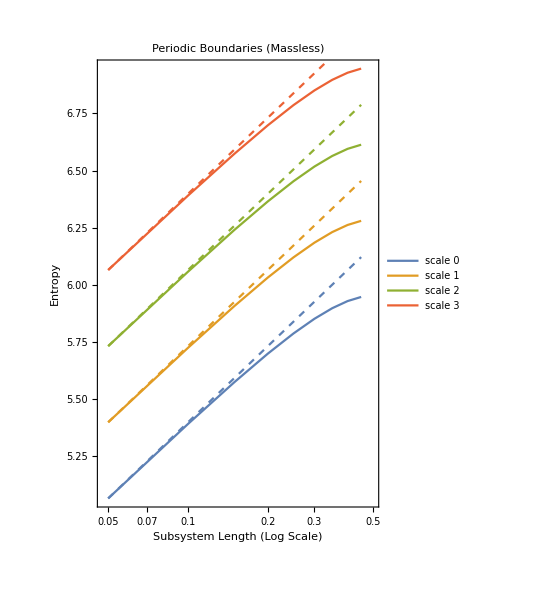

```mathematica
With[{multiplier=1/3,numOfScales=4},
constantTermBosonic[scaleIndex_]:=data[[scaleIndex,1,2]]-multiplier*Log2[data[[scaleIndex,1,1]]];
fitEntropyFunctionBosonic[scaleIndex_]:=multiplier*Log2[#]+constantTermBosonic[scaleIndex]&;

fitEntropyPlotBosonic=LogLinearPlot[
Evaluate@Table[fitEntropyFunctionBosonic[scaleIndex+1][subsystemModes],{scaleIndex,0,numOfScales-1}],
{subsystemModes,data[[1,1,1]],data[[1,-1,1]]},
PlotStyle->Dashed
];

entropyPlotBosonic=ListLogLinearPlot[data,
Joined->True,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->3/2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,5,1,-1}],None}},
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subsystem Length (Log Scale)","Entropy"},
PlotLabel->Style["Periodic Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("scale "<>ToString[#]&/@Range[0,numOfScales-1])
];

Show[entropyPlotBosonic,fitEntropyPlotBosonic]
]
```

## Bosonic Entanglement Entropy Plots (Open Boundary)

Computation of entropies at scale 0 finished in 0 seconds.

Computation of entropies at scale 1 finished in 0 seconds.

Computation of entropies at scale 2 finished in 1 seconds.

Computation of entropies at scale 3 finished in 3 seconds.

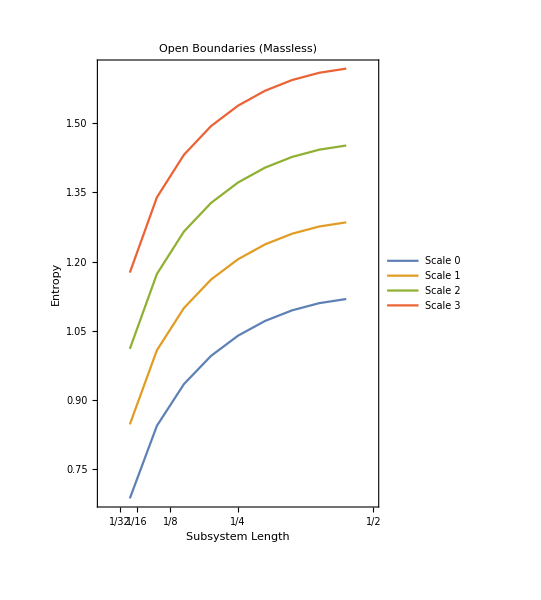

```mathematica
With[{dbIndex=3,boundary="open",mass=0,baseScaleModes=100,stepModes=5,numOfScales=4},
data=Table[0,{numOfScales}];
genData=genEntropyTableBosonic[dbIndex,mass,boundary];

Clear[tic,toc];
Do[
tic=AbsoluteTime[];
With[{maxScale=scaleIndex-1},
data[[scaleIndex]]=genData[baseScaleModes,maxScale,stepModes*2^maxScale]];
toc=AbsoluteTime[];
Print["Computation of entropies at scale ",scaleIndex-1," finished in ",Round[toc-tic]," seconds."],
{scaleIndex,numOfScales}];

ListPlot[data,
Joined->True ,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->3/2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,5,1,-1}],None}},
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subsystem Length","Entropy"},
PlotLabel->Style["Open Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("Scale "<>ToString[#]&/@Range[0,numOfScales-1])]
]
```

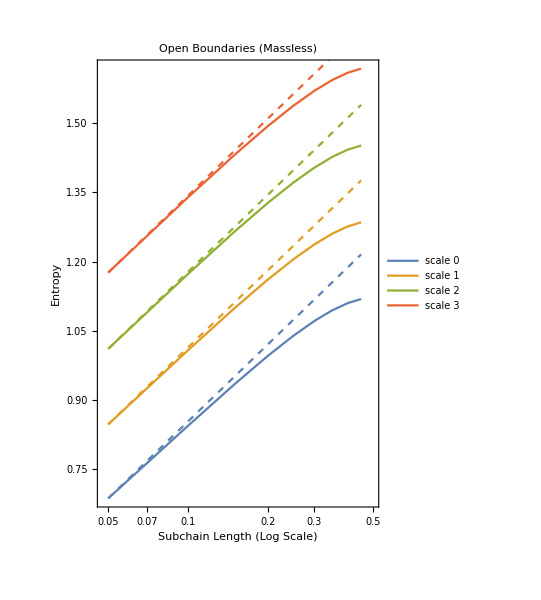

```mathematica
With[{multiplier=1/6,numOfScales=4},
constantTermBosonic[scaleIndex_]:=data[[scaleIndex,1,2]]-multiplier*Log2[data[[scaleIndex,1,1]]];
fitEntropyFunctionBosonic[scaleIndex_]:=multiplier*Log2[#]+constantTermBosonic[scaleIndex]&;

fitEntropyPlotBosonic=LogLinearPlot[
Evaluate@Table[fitEntropyFunctionBosonic[scaleIndex+1][subsystemModes],{scaleIndex,0,numOfScales-1}],
{subsystemModes,data[[1,1,1]],data[[1,-1,1]]},
PlotStyle->Dashed
];

entropyPlotBosonic=ListLogLinearPlot[data,
Joined->True,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->3/2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,5,1,-1}],None}},
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subchain Length (Log Scale)","Entropy"},
PlotLabel->Style["Open Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("scale "<>ToString[#]&/@Range[0,numOfScales-1])
];

Show[entropyPlotBosonic,fitEntropyPlotBosonic]
]
```

# Fermionic Theory

## Fermionic Coupling Matrix in Fixed-Scale Wavelet Basis

```mathematica
coupMtxFermionic[waveletIndex_Integer/;waveletIndex≥3,mass_?NumericQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],
prec_:MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer]:=
With[
{P=2^scaleIndex*derivativeMtx[waveletIndex,1,boundary][baseScaleModes*2^scaleIndex],
M=mass*sparseIdentityMtx[baseScaleModes*2^scaleIndex],
zMtx=zeroMtx[baseScaleModes*2^scaleIndex]
},
ArrayFlatten[
{{zMtx,P-M},
{P+M,zMtx}}]
];
```

```mathematica
With[{dbIndex=3,boundary="open",minResolution=10,maxScale=0,mass=.1},
coupMtxFermionic[dbIndex,mass,boundary][minResolution,maxScale]//MatrixForm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.745205 | -0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.145205 | 0.745205 | -0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0146119 | -0.145205 | 0.745205 | -0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | -0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | -0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | -0.1 | -0.745205 | 0.145205 | -0.0146119
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | -0.1 | -0.745205 | 0.145205
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | -0.1 | -0.745205
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | -0.1
0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.745205 | 0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.145205 | 0.745205 | 0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0146119 | -0.145205 | 0.745205 | 0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.000342466 | 0.0146119 | -0.145205 | 0.745205 | 0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | 0.1 | -0.745205 | 0.145205 | -0.0146119 | -0.000342466 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | 0.1 | -0.745205 | 0.145205 | -0.0146119 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | 0.1 | -0.745205 | 0.145205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | 0.1 | -0.745205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0.000342466 | 0.0146119 | -0.145205 | 0.745205 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Fermionic Subsystem Covariance Matrix

```mathematica
covMtxFermionic[waveletIndex_Integer/;waveletIndex≥3,mass_?NumericQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],
Prec_:MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer]:=
Module[{R,size=2*baseScaleModes*2^scaleIndex},
With[{Q=N[coupMtxFermionic[waveletIndex,mass,boundary][baseScaleModes,scaleIndex],Prec]},
R=symplecticDiagonalization[Q]
];
Transpose[R].symplecticMtx[size].R
];
(* prec in above block is used to convert rational nuumberts to decimal form *)


covMtxSymplecticDiags[waveletIndex_Integer/;waveletIndex≥3,mass_?NumericQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],
Prec_:MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer] :=
Module[
{upRightBlock,bottomLeftBlock,covMtx= covMtxFermionic[waveletIndex,mass,boundary][baseScaleModes,scaleIndex],size=2*baseScaleModes*2^scaleIndex},
upRightBlock=covMtx[[1;;size/2,size/2+1;;size]];
bottomLeftBlock=covMtx[[size/2+1;;size,1;;size/2]];
{upRightBlock,bottomLeftBlock}];


sysCovMtxFermionic[covMtxSympDiags_]:=blockAntiDiagMtx[covMtxSympDiags];
subsysCovMtxFermionic[covMtxSympDiags_][modeList_]:=blockAntiDiagMtx[#[[modeList,modeList]]&/@covMtxSympDiags];
```

```mathematica
With[{dbIndex=3,boundary="periodic",mass=.1,minResolution=5,maxScale=0},
Chop[covMtxFermionic[dbIndex,mass,boundary][minResolution,maxScale]]//MatrixForm
]
```

(0 | 0 | 0 | 0 | 0 | -0.403097 | -0.838878 | -0.230803 | -0.239253 | -0.152589
0 | 0 | 0 | 0 | 0 | 0.72344 | -0.116568 | -0.63547 | -0.0445304 | -0.239253
0 | 0 | 0 | 0 | 0 | -0.371255 | 0.507347 | -0.384287 | -0.63547 | -0.230803
0 | 0 | 0 | 0 | 0 | 0.156391 | -0.0289023 | 0.507347 | -0.116568 | -0.838878
0 | 0 | 0 | 0 | 0 | -0.389691 | 0.156391 | -0.371255 | 0.72344 | -0.403097
0.403097 | -0.72344 | 0.371255 | -0.156391 | 0.389691 | 0 | 0 | 0 | 0 | 0
0.838878 | 0.116568 | -0.507347 | 0.0289023 | -0.156391 | 0 | 0 | 0 | 0 | 0
0.230803 | 0.63547 | 0.384287 | -0.507347 | 0.371255 | 0 | 0 | 0 | 0 | 0
0.239253 | 0.0445304 | 0.63547 | 0.116568 | -0.72344 | 0 | 0 | 0 | 0 | 0
0.152589 | 0.239253 | 0.230803 | 0.838878 | 0.403097 | 0 | 0 | 0 | 0 | 0)

```mathematica
With[{dbIndex=3,boundary="periodic",mass=.1,minResolution=5,maxScale=0},
covMtxSymplecticDiags[dbIndex,mass,boundary][minResolution,maxScale]//MatrixForm
]
```

((-0.403097
-0.838878
-0.230803
-0.239253
-0.152589) | (0.72344
-0.116568
-0.63547
-0.0445304
-0.239253) | (-0.371255
0.507347
-0.384287
-0.63547
-0.230803) | (0.156391
-0.0289023
0.507347
-0.116568
-0.838878) | (-0.389691
0.156391
-0.371255
0.72344
-0.403097)
(0.403097
-0.72344
0.371255
-0.156391
0.389691) | (0.838878
0.116568
-0.507347
0.0289023
-0.156391) | (0.230803
0.63547
0.384287
-0.507347
0.371255) | (0.239253
0.0445304
0.63547
0.116568
-0.72344) | (0.152589
0.239253
0.230803
0.838878
0.403097))

```mathematica
With[{covMtxSympDiags=covMtxSymplecticDiags[3,1,"periodic"],minResolution=5,maxScale=0},
sysCovMtxFermionic[covMtxSympDiags[minResolution,maxScale]]//MatrixForm
]
```

(0 | 0 | 0 | 0 | 0 | -0.833779 | -0.548171 | -0.0507188 | -0.041812 | -0.0000403913
0 | 0 | 0 | 0 | 0 | 0.498323 | -0.708808 | -0.49564 | -0.0431218 | -0.041812
0 | 0 | 0 | 0 | 0 | -0.199239 | 0.40914 | -0.738023 | -0.49564 | -0.0507188
0 | 0 | 0 | 0 | 0 | 0.102014 | -0.138916 | 0.40914 | -0.708808 | -0.548171
0 | 0 | 0 | 0 | 0 | -0.0798993 | 0.102014 | -0.199239 | 0.498323 | -0.833779
0.833779 | -0.498323 | 0.199239 | -0.102014 | 0.0798993 | 0 | 0 | 0 | 0 | 0
0.548171 | 0.708808 | -0.40914 | 0.138916 | -0.102014 | 0 | 0 | 0 | 0 | 0
0.0507188 | 0.49564 | 0.738023 | -0.40914 | 0.199239 | 0 | 0 | 0 | 0 | 0
0.041812 | 0.0431218 | 0.49564 | 0.708808 | -0.498323 | 0 | 0 | 0 | 0 | 0
0.0000403913 | 0.041812 | 0.0507188 | 0.548171 | 0.833779 | 0 | 0 | 0 | 0 | 0)

```mathematica
With[{covMtxSympDiag=covMtxSymplecticDiags[3,1,"periodic"],minResolution=5,maxScale=0},
subsysCovMtxFermionic[covMtxSympDiag[minResolution,maxScale]][Range[3]]//MatrixForm
]
```

(0 | 0 | 0 | -0.833779 | -0.548171 | -0.0507188
0 | 0 | 0 | 0.498323 | -0.708808 | -0.49564
0 | 0 | 0 | -0.199239 | 0.40914 | -0.738023
0.833779 | -0.498323 | 0.199239 | 0 | 0 | 0
0.548171 | 0.708808 | -0.40914 | 0 | 0 | 0
0.0507188 | 0.49564 | 0.738023 | 0 | 0 | 0)

## Fermionic Subsystem Entanglement Entropy

```mathematica
subsysEntropyFermionic[subsysCovMtx_?MatrixQ]:=
With[
{fermionicEntropyFunc=If[0<= #<1,-((1+#)/2)Log2[(1+#)/2]-((1-#)/2)Log2[(1-#)/2],0] &},
Total[fermionicEntropyFunc/@Im[Eigenvalues[subsysCovMtx]]]
]
```

```mathematica
With[
{covMtxDiags=covMtxSymplecticDiags[3,10^-6,"open"],minResolution=50,maxScale=0},
With[
{covMtx=subsysCovMtxFermionic[covMtxDiags[minResolution,maxScale]],system=All,subsystem=Range[minResolution/2]},
Print["Eigenvalues of system's covariance matrix: ",Im[Eigenvalues[covMtx[system]]]];
Print["Eigenvalues of subsystem's covariance matrix: ",Im[Eigenvalues[covMtx[subsystem]]]];
Print["Entropy of whole system: ",subsysEntropyFermionic[covMtx[system]]];
Print["Entropy of subsystem: ",subsysEntropyFermionic[covMtx[subsystem]]]
]
]
```

Eigenvalues of system's covariance matrix: {1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.}

Eigenvalues of subsystem's covariance matrix: {1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,0.999996,-0.999996,0.999996,-0.999996,0.999277,-0.999277,0.999277,-0.999277,0.940084,-0.940084,0.940082,-0.940082,0.0000131049,-0.0000131049}

Entropy of whole system: 0

Entropy of subsystem: 1.39776

## Generating Data for Fermionic Entanglement Entropy

```mathematica
genEntropyTableFermionic[waveletIndex_Integer/;waveletIndex≥3,mass_?NumberQ,
boundary_String/;StringMatchQ[boundary,{"open","periodic","antiperiodic"}],
prec_:MachinePrecision][baseScaleModes_Integer,scaleIndex_Integer,stepModes_Integer]:=
With[
{covSympDiags=covMtxSymplecticDiags[waveletIndex,mass,boundary,prec][baseScaleModes,scaleIndex],systemModes=baseScaleModes*2^scaleIndex},
Block[{subsystemModes},
Monitor[
Table[{subsystemModes/systemModes,subsysEntropyFermionic[subsysCovMtxFermionic[covSympDiags][Range[subsystemModes]]]},
{subsystemModes,stepModes,systemModes/2-stepModes,stepModes}],
ProgressIndicator[subsystemModes/systemModes]]
]];
```

## Fermionic Entanglement Entropy Plots (Periodic Boundary)

Computation of entropies at scale 0 finished in 0 seconds.

Eigensystem::arh: Because finding 200 out of the 200 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Computation of entropies at scale 1 finished in 0 seconds.

Eigensystem::arh: Because finding 400 out of the 400 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Computation of entropies at scale 2 finished in 0 seconds.

Eigensystem::arh: Because finding 800 out of the 800 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

Computation of entropies at scale 3 finished in 2 seconds.

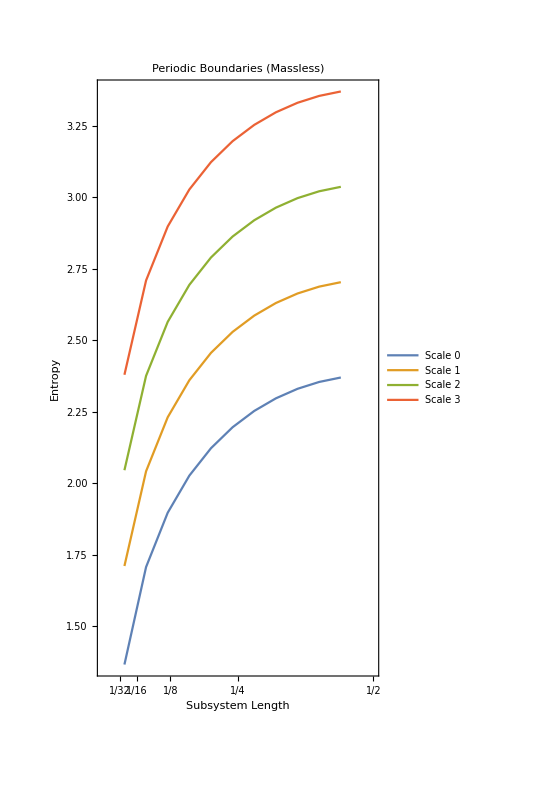

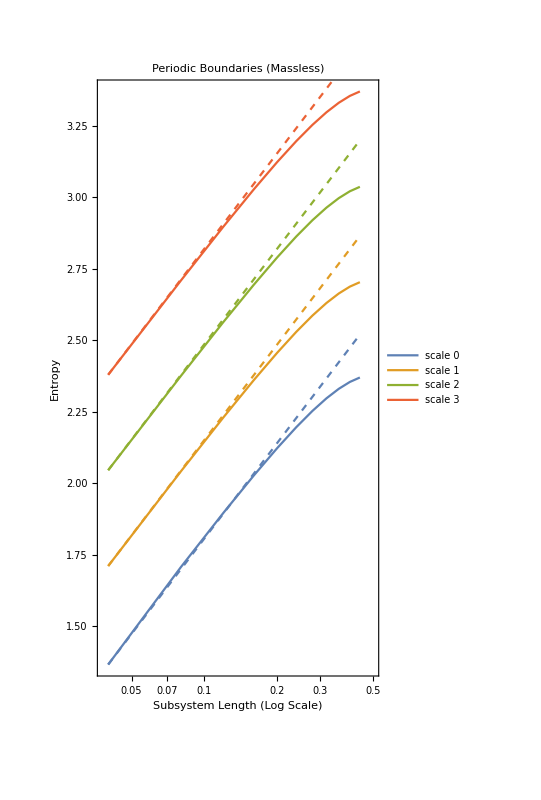

```mathematica
With[{dbIndex=3,boundary="periodic",baseScaleModes=50,mass=10^-8,stepModes=2,numOfScales=4,multiplier=1/3},
data=Table[0,{numOfScales}];
genData=genEntropyTableFermionic[dbIndex,mass,boundary];
constantTermFermionic[scaleIndex_]:=data[[scaleIndex,1,2]]-multiplier*Log2[data[[scaleIndex,1,1]]];
fitFuncFermionic[scaleIndex_]:=multiplier*Log2[#]+constantTermFermionic[scaleIndex]&;

Clear[tic,toc];

Do[
tic=AbsoluteTime[];
With[{maxScale=scaleIndex-1},data[[scaleIndex]]=genData[baseScaleModes,maxScale,stepModes*2^maxScale]];
toc=AbsoluteTime[];
Print["Computation of entropies at scale ",scaleIndex-1," finished in ",Round[toc-tic]," seconds."],
{scaleIndex,numOfScales}];

entropyPlotFermionic=ListPlot[data,
Joined->True ,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,5,1,-1}],None}},
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subsystem Length","Entropy"},
PlotLabel->Style["Periodic Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("Scale "<>ToString[#]&/@Range[0,numOfScales-1])];


entropyPlotLogScaleFermionic=ListLogLinearPlot[data,
Joined->True ,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,6,1,-1}],None}},
(*FrameTicks->{{Automatic,None},{{#,InputForm[#]}&/@Table[2^(-i),{i,6,1,-1}],None}}, * / for divisions *)
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subsystem Length (Log Scale)","Entropy"},
PlotLabel->Style["Periodic Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("scale "<>ToString[#]&/@Range[0,numOfScales-1])
];

fitPlotFermionic=LogLinearPlot[
Evaluate@Table[fitFuncFermionic[scaleIndex+1][subsystemModes],{scaleIndex,0,numOfScales-1}],
{subsystemModes,data[[1,1,1]],data[[1,-1,1]]},
PlotStyle->Dashed
];
]
Show[entropyPlotFermionic]
Show[entropyPlotLogScaleFermionic,fitPlotFermionic]
```

## Fermionic Entanglement Entropy Plots (Open Boundary)

Eigensystem::arh: Because finding 200 out of the 200 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Computation of entropies at scale 0 finished in 0 seconds.

Eigensystem::arh: Because finding 400 out of the 400 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Computation of entropies at scale 1 finished in 0 seconds.

Eigensystem::arh: Because finding 800 out of the 800 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

Computation of entropies at scale 2 finished in 2 seconds.

Computation of entropies at scale 3 finished in 12 seconds.

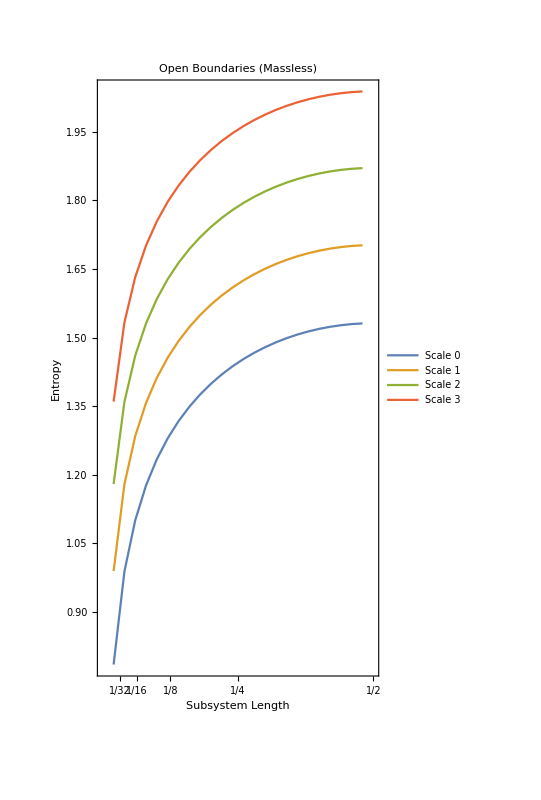

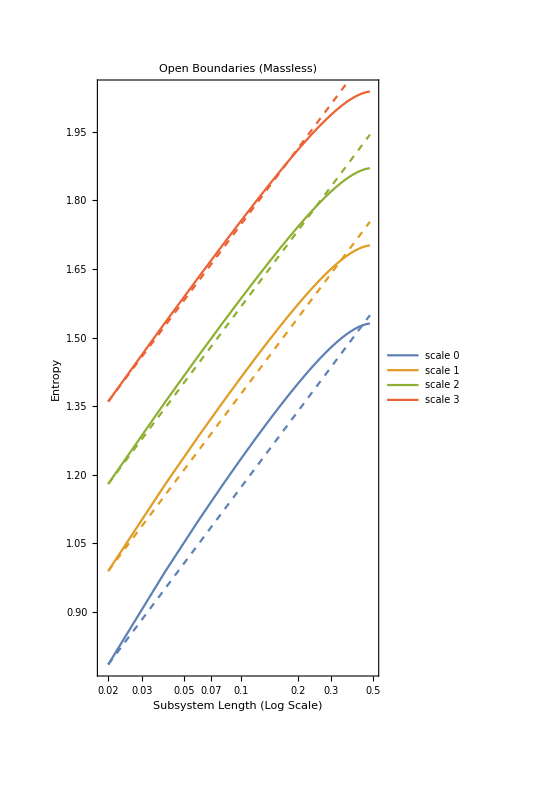

```mathematica
With[{dbIndex=3,boundary="open",baseScaleModes=100,mass=0,stepModes=2,numOfScales=4,multiplier=1/6},
data=Table[0,{numOfScales}];
genData=genEntropyTableFermionic[dbIndex,mass,boundary];
constantTermFermionic[scaleIndex_]:=data[[scaleIndex,1,2]]-multiplier*Log2[data[[scaleIndex,1,1]]];
fitFuncFermionic[scaleIndex_]:=multiplier*Log2[#]+constantTermFermionic[scaleIndex]&;

Clear[tic,toc];

Do[
tic=AbsoluteTime[];
With[{maxScale=scaleIndex-1},data[[scaleIndex]]=genData[baseScaleModes,maxScale,stepModes*2^maxScale]];
toc=AbsoluteTime[];
Print["Computation of entropies at scale ",scaleIndex-1," finished in ",Round[toc-tic]," seconds."],
{scaleIndex,numOfScales}];

entropyPlotFermionic=ListPlot[data,
Joined->True ,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,5,1,-1}],None}},
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subsystem Length","Entropy"},
PlotLabel->Style["Open Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("Scale "<>ToString[#]&/@Range[0,numOfScales-1])];


entropyPlotLogScaleFermionic=ListLogLinearPlot[data,
Joined->True ,Frame->True,FrameStyle->Black,
PlotRange->{{0,1/2},Automatic},
AxesOrigin->{0,data[[1,1,2]]},
AspectRatio->2,
FrameTicks->{{Automatic,None},{Table[2^(-j),{j,6,1,-1}],None}},
(*FrameTicks->{{Automatic,None},{{#,InputForm[#]}&/@Table[2^(-i),{i,6,1,-1}],None}}, * / for divisions *)
LabelStyle->{FontFamily->"Times",FontSize->12},
FrameLabel->{"Subsystem Length (Log Scale)","Entropy"},
PlotLabel->Style["Open Boundaries (Massless)",FontSize->12,Black,FontFamily->"Times"],
PlotLegends->("scale "<>ToString[#]&/@Range[0,numOfScales-1])
];

fitPlotFermionic=LogLinearPlot[
Evaluate@Table[fitFuncFermionic[scaleIndex+1][subsystemModes],{scaleIndex,0,numOfScales-1}],
{subsystemModes,data[[1,1,1]],data[[1,-1,1]]},
PlotStyle->Dashed
];
]
Show[entropyPlotFermionic]
Show[entropyPlotLogScaleFermionic,fitPlotFermionic]
```